# Wave Function CFD

## Tyler’s Coefficients

```mathematica
(*Trying to find a good method for storing and indexing Tyler's coefficients*)

(*
LHS,
1  α12 β12 0  0  0  0 ...,
α21 1  α22 β22 0  0  0 ...,
β31 α31 1  α32 β32 0  0 ...,

... 0  β  α  1  α  β 0 ..., 

... 0  0  0  β3 α3 1  α3 β3,
... 0  0  0  0  β2 α2 1  α2,
... 0  0  0  0  0  β1 α1 1 ,

RHS,
1  α1 β1 0  0  0  0 ...,
α2 1  α2 β2 0  0  0 ...,
β3 α3 1  α3 β3 0  0 ...,

... 0  β  α  1  α  β 0 ..., 

... 0  0  0  β3 α3 1  α3 β3,
... 0  0  0  0  β2 α2 1  α2,
... 0  0  0  0  0  β1 α1 1 ,

*)

αterms={
{α12,β12},
{α21,α22,β22},
{β31,α31,α32,β32},
{β41,α41,α42,β42},
};
aterms={
{a1,b1,c1,d1,e1,f1,g1,h1,i1,j1,k1},
{a2,b2,c2,d2,e2,f2,g2,h2,i2,j2,k2},
{a3,b3,c3,d3,e3,f3,g3,h3,i3,j3,k3},
{a4,b4,c4,d4,e4,f4,g4,h4,i4,j4,k4}
};
coeffVariables={
α,β,
α12,β12,
α21,α22,β22,
β31,α31,α32,β32,
β41,α41,α42,β42,
a,b,c,d,
a1,b1,c1,d1,e1,f1,g1,h1,i1,j1,k1,
a2,b2,c2,d2,e2,f2,g2,h2,i2,j2,k2,
a3,b3,c3,d3,e3,f3,g3,h3,i3,j3,k3,
a4,b4,c4,d4,e4,f4,g4,h4,i4,j4,k4
};

coeffT4={α->1/4,α1->3,a1->-17/6,a2->3/2,a3->3/2,a4->-1/6};

coeffP12={
α->8/15,β->1/15,
α12->20,β12->45,
α21->1/27,α22->4,β22->28/9,
β31->1/168,α31->4/21,α32->4/3,β32->5/12,
β41->1/42,α41->1/3,α42->5/6,β42->1/6,
a->308/225,b->182/225,c->4/175,d->-1/1575,
a1->-1590/359,b1->-4609/126,c1->711/56,d1->40,e1->-35/2,f1->42/5,g1->-7/2,h1->8/7,i1->-15/56,j1->5/126,k1->-1/360,
a2->-857/4963,b2->-621/280,c2->-83/35,d2->511/135,e2->7/6,f2->-7/30,g2->7/135,h2->-1/105,i2->1/840,j2->-1/13608,k2->0,
a3->-115/4024,b3->-1019/2205,c3->-19/20,d3->23/45,e3->125/144,f3->1/15,g3->-1/180,h3->1/2205,i3->-1/47040,j3->0,k3->0,
a4->-1/1680,b4->-193/2205,c4->-107/180,d4->-9/20,e4->25/36,f4->19/45,g4->1/60,h4->-1/1260,i4->1/35280,j4->0,k4->0
};
```

## Animated

```mathematica
Clear["`*"];

(*Define Variables*)
Δt=0.01;
c=0.05;
n=100;
h=1/(n-1);
timeSteps=10/Δt;
fps=1/Δt;

(*Create function initial condition as discrete list*)
ϕ=Array[Sin[10π#]&,n,{0,1}];

(*Generate the LHS Matrix for the CFD*)
LHSRow[i_,j_]:=Module[{},
If[i==j,1,If[i==j+1 ||i==j-1,1/4,0]]
]
LHS=Array[LHSRow[#1,#2]&,{n,n}];
LHS//MatrixForm;

(*Generate the RHS Matrix for the CFD*)
RHSRow[i_,j_]:=Module[{},
If[i==j(*||i==1||i==n*),0,If[i==j+1,-3/(4h),If[i==j-1,3/(4h),0]]]
]
RHS=Array[RHSRow[#1,#2]&,{n,n}];
RHS//MatrixForm;

(*Find the Inverse of the LHS Matrix*)
inverseLHS=Inverse[LHS];

(*Create discrete list of the function progressing through time*)
ϕT={ϕ};

For[i=0,i<timeSteps,i++,
(*Calculate the function at the next time step using the CFD*)
last=ϕT[[Length[ϕT]]];
new=last-c Δt inverseLHS.RHS.last;
ϕT=Append[ϕT,new];

(*Force the boundary conditions*)
(*ϕT[[Length[ϕT]]][[1]]=0;*)
]

(*Generate a select list of Plots from the total discrete list of functions through time*)
plots={};
numPlots=50;
For[i=0,i<=numPlots,i++,
plots=Append[plots,ListPlot[ϕT[[Floor[Max[i*Length[ϕT]/numPlots,1]]]],PlotRange->{-2,2},Joined->False]];
]

(*Animate the Plots*)
ListAnimate[plots,fps*numPlots/timeSteps]
```

## Static - No Boundary Conditions

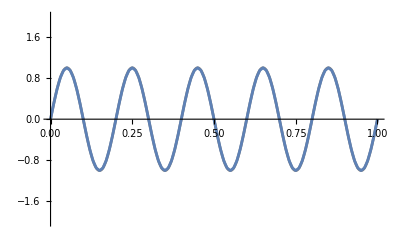

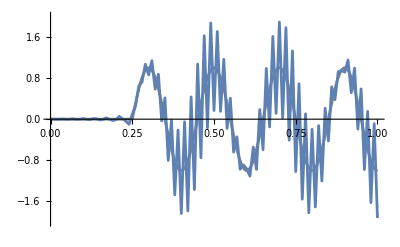

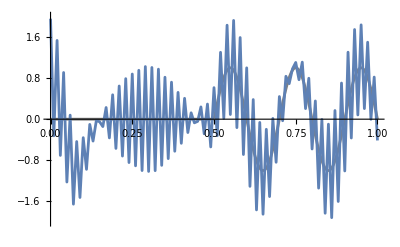

```mathematica
Clear["`*"];

(*Define Variables*)
Δt=0.001;
c=0.05;
n=101;
h=1/(n-1);
timeSteps=10/Δt;

(*Create function initial condition as discrete list*)
ϕ=Array[Sin[10π#]&,n,{0,1}];

ϕTrue[x_,t_]:=If[x>c t,Sin[10π (x-c t)],0];

(*Generate the LHS Matrix for the CFD*)
LHSRow[i_,j_]:=Module[{},
If[i==j,1,If[i==j+1||i==j-1,1/4,0]]
]
LHS=Array[LHSRow[#1,#2]&,{n,n}];
LHS//MatrixForm;

(*Generate the RHS Matrix for the CFD*)
RHSRow[i_,j_]:=Module[{},
If[j==i-1,-3/(4 h),If[j==i+1,3/(4 h),0]]
]
RHS=Array[RHSRow[#1,#2]&,{n,n}];
RHS//MatrixForm;

(*Find the Inverse of the LHS Matrix and the Q matrix*)
inverseLHS=Inverse[LHS];
Q=inverseLHS.RHS;

timeVal=0;

updateFunction[steps_]:=Module[{},
For[i=0,i<steps,i++,
timeVal+=Δt;
ϕ=ϕ-c Δt Q.ϕ;

(*
ϕ[[n]]=ϕTrue[n,timeVal];
ϕ[[n-1]]=ϕTrue[n-1h,timeVal];
ϕ[[n-2]]=ϕTrue[n-2h,timeVal];*)
];
]
plotFunction[]:=Module[{},
normalizePlot={};
For[i=1,i<=n,i++,AppendTo[normalizePlot,{(i-1)/(n-1),ϕ[[i]]}]];
Show[Plot[ϕTrue[x,timeVal],{x,0,1},PlotRange->{-2,2},PlotStyle->Gray],
ListPlot[normalizePlot,PlotRange->{-2,2},Joined->True]]
]

plotFunction[]

updateFunction[timeSteps/2]
plotFunction[]

updateFunction[timeSteps/2]
plotFunction[]
```

## Static - With Fixed Left and Absorbing Right Boundary Conditions

-Graphics-

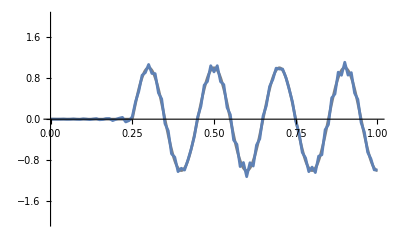

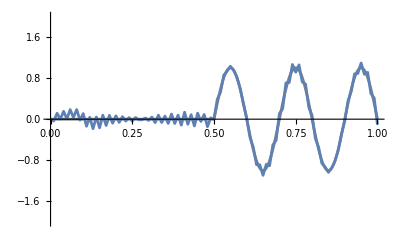

```mathematica
Clear["`*"];

(*Define Variables*)
Δt=0.001;
c=0.05;
n=101;
h=1/(n-1);
timeSteps=10/Δt;

(*Create function initial condition as discrete list*)
ϕ=Array[Sin[10π#]&,n,{0,1}];

ϕTrue[x_,t_]:=If[x>c t,Sin[10π (x-c t)],0];

(*Generate the LHS Matrix for the CFD*)
LHSRow[i_,j_]:=Module[{},
If[i==1&&j==1,1,
If[i==j,1,If[(i==j+1||i==j-1)&&i>1,1/4,0]
]
]
]
LHS=Array[LHSRow[#1,#2]&,{n,n}];
LHS//MatrixForm;

(*Generate the RHS Matrix for the CFD*)
RHSRow[i_,j_]:=Module[{},
If[i==1,0,
If[i==n,
If[j==n-1,-3/(4 h),If[j==n,3/(4 h),0]],
If[j==i-1,-3/(4 h),If[j==i+1,3/(4 h),0]]
]
]
]
RHS=Array[RHSRow[#1,#2]&,{n,n}];
RHS//MatrixForm;

(*Find the Inverse of the LHS Matrix and the Q matrix*)
inverseLHS=Inverse[LHS];
Q=inverseLHS.RHS;

timeVal=0;

updateFunction[steps_]:=Module[{},
For[i=0,i<steps,i++,
timeVal+=Δt;
ϕ=ϕ-c Δt Q.ϕ;

(*
ϕ[[n]]=ϕTrue[n,timeVal];
ϕ[[n-1]]=ϕTrue[n-1h,timeVal];
ϕ[[n-2]]=ϕTrue[n-2h,timeVal];*)
];
]
plotFunction[]:=Module[{},
normalizePlot={};
For[i=1,i<=n,i++,AppendTo[normalizePlot,{(i-1)/(n-1),ϕ[[i]]}]];
Show[Plot[ϕTrue[x,timeVal],{x,0,1},PlotRange->{-2,2},PlotStyle->Gray],
ListPlot[normalizePlot,PlotRange->{-2,2},Joined->True]]
]

plotFunction[]

updateFunction[timeSteps/2]
plotFunction[]

updateFunction[timeSteps/2]
plotFunction[]
```

## Static - Forced Analytic Right Boundary

-Graphics-

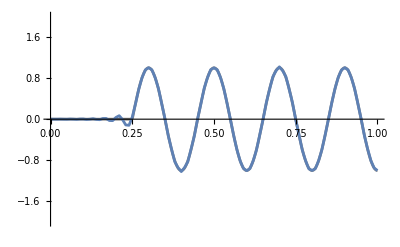

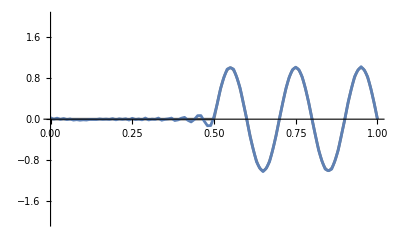

```mathematica
Clear["`*"];

(*Define Variables*)
Δt=0.001;
c=0.05;
n=101;
h=1/(n-1);
timeSteps=10/Δt;

(*Create function initial condition as discrete list*)
ϕ=Array[Sin[10π#]&,n,{0,1}];

ϕTrue[x_,t_]:=If[x>c t,Sin[10π (x-c t)],0];

(*Generate the LHS Matrix for the CFD*)
LHSRow[i_,j_]:=Module[{},
If[i==1&&j==1,1,
If[i==j,1,If[(i==j+1||i==j-1)&&i>1,1/4,0]
]
]
]
LHS=Array[LHSRow[#1,#2]&,{n,n}];
LHS//MatrixForm;

(*Generate the RHS Matrix for the CFD*)
RHSRow[i_,j_]:=Module[{},
If[j==i-1,-3/(4 h),If[j==i+1,3/(4 h),0]]
]
RHS=Array[RHSRow[#1,#2]&,{n,n}];
RHS//MatrixForm;

(*Find the Inverse of the LHS Matrix and the Q matrix*)
inverseLHS=Inverse[LHS];
Q=inverseLHS.RHS;

timeVal=0;

updateFunction[steps_]:=Module[{},
For[i=0,i<steps,i++,
timeVal+=Δt;
ϕ=ϕ-c Δt Q.ϕ;

(*Force the 3 rightmost points to be equal to the analytic solution*)
ϕ[[n]]=ϕTrue[n,timeVal];
ϕ[[n-1]]=ϕTrue[n-1h,timeVal];
ϕ[[n-2]]=ϕTrue[n-2h,timeVal];
];
]
plotFunction[]:=Module[{},
normalizePlot={};
For[i=1,i<=n,i++,AppendTo[normalizePlot,{(i-1)/(n-1),ϕ[[i]]}]];
Show[Plot[ϕTrue[x,timeVal],{x,0,1},PlotRange->{-2,2},PlotStyle->Gray],
ListPlot[normalizePlot,PlotRange->{-2,2},Joined->True]]
]

plotFunction[]

updateFunction[timeSteps/2]
plotFunction[]

updateFunction[timeSteps/2]
plotFunction[]
```

## Static - Fixed Left and T4 Right Boundary Conditions

-Graphics-

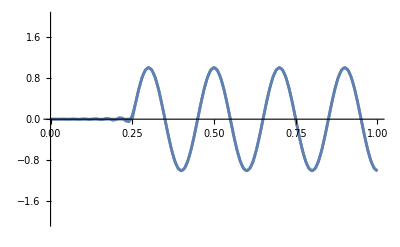

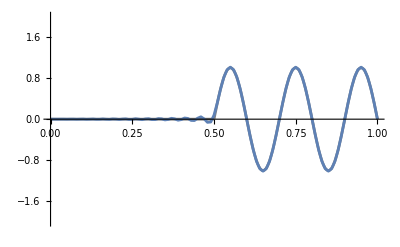

```mathematica
Clear["`*"];

(*Define Variables*)
Δt=0.001;
c=0.05;
n=101;
h=1/(n-1);
timeSteps=10/Δt;

(*Create function initial condition as discrete list*)
ϕ=Array[Sin[10π#]&,n,{0,1}];

ϕTrue[x_,t_]:=If[x>c t,Sin[10π (x-c t)],0];

coeffT4={α->1/4,γ->3,a1->-17/6,a2->3/2,a3->3/2,a4->-1/6};

(*Generate the LHS Matrix for the CFD*)
LHSRow[i_,j_]:=Module[{},
If[i==1&&j==1,1,
If[(i==n&&j==n-1),γ,
If[i==j,1,If[(i==j+1||i==j-1)&&i>1,α,0]
]
]
]
]
LHS=Array[LHSRow[#1,#2]&,{n,n}]/.coeffT4;
LHS//MatrixForm;

terms={a1,a2,a3,a4};

(*Generate the RHS Matrix for the CFD*)
RHSRow[i_,j_]:=Module[{},
If[i==1&&j<5,0,
If[i==n&&j>n-4,-terms[[n-j+1]]/h,
If[j==i-1,-3/(4 h),If[j==i+1,3/(4 h),0]]
]
]
]
RHS=Array[RHSRow[#1,#2]&,{n,n}]/.coeffT4;
RHS//MatrixForm;

(*Find the Inverse of the LHS Matrix and the Q matrix*)
inverseLHS=Inverse[LHS];
Q=inverseLHS.RHS;
Q//MatrixForm;

timeVal=0;

updateFunction[steps_]:=Module[{},
For[i=0,i<steps,i++,
timeVal+=Δt;
ϕ=ϕ-c Δt Q.ϕ;
];
]
plotFunction[]:=Module[{},
normalizePlot={};
For[i=1,i<=n,i++,AppendTo[normalizePlot,{(i-1)/(n-1),ϕ[[i]]}]];
Show[Plot[ϕTrue[x,timeVal],{x,0,1},PlotRange->{-2,2},PlotStyle->Gray],
ListPlot[normalizePlot,PlotRange->{-2,2},Joined->True]]
]

plotFunction[]

updateFunction[timeSteps/2]
plotFunction[]

updateFunction[timeSteps/2]
plotFunction[]
```

## Static - Generalized

```mathematica
Clear["`*"];

(*Define Variables*)
Δt=0.001;
cc=0.05;
n=101;
h=1/(n-1);
timeSteps=10/Δt; (*numeric value should be in seconds*)

(*Create wave function initial condition as discrete list*)
ϕ=Array[Sin[10π#]&,n,{0,1}];

ϕTrue[x_,t_]:=If[x>cc t,Sin[10π (x-cc t)],0];

coeffT4={α->1/4,γ->3,a1->-17/6,a2->3/2,a3->3/2,a4->-1/6};


coeffP12={
α->8/15,β->1/15,
α12->20,β12->45,
α21->1/27,α22->4,β22->28/9,
β31->1/168,α31->4/21,α32->4/3,β32->5/12,
β41->1/42,α41->1/3,α42->5/6,β42->1/6,
a->308/225,b->182/225,c->4/175,d->-1/1575,
a1->-1590/359,b1->-4609/126,c1->711/56,d1->40,e1->-35/2,f1->42/5,g1->-7/2,h1->8/7,i1->-15/56,j1->5/126,k1->-1/360,
a2->-857/4963,b2->-621/280,c2->-83/35,d2->511/135,e2->7/6,f2->-7/30,g2->7/135,h2->-1/105,i2->1/840,j2->-1/13608,k2->0,
a3->-115/4024,b3->-1019/2205,c3->-19/20,d3->23/45,e3->125/144,f3->1/15,g3->-1/180,h3->1/2205,i3->-1/47040,j3->0,k3->0,
a4->-1/1680,b4->-193/2205,c4->-107/180,d4->-9/20,e4->25/36,f4->19/45,g4->1/60,h4->-1/1260,i4->1/35280,j4->0,k4->0
};


LHSBorders={
{1,α12,β12},
{α21,1,α22,β22},
{β31,α31,1,α32,β32},
{0,β41,α41,1,α42,β42},
};
RHSBorders={
{a1,b1,c1,d1,e1,f1,g1,h1,i1,j1,k1},
{a2,b2,c2,d2,e2,f2,g2,h2,i2,j2,k2},
{a3,b3,c3,d3,e3,f3,g3,h3,i3,j3,k3},
{a4,b4,c4,d4,e4,f4,g4,h4,i4,j4,k4}
};

LHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->1,
Band[{2,1}]->α,
Band[{1,2}]->α,
Band[{3,1}]->β,
Band[{1,3}]->β
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[LHSBorders[[i]]],j++,
M[[i,j]]=LHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=LHSBorders[[i,j]]/.coeff
]
];

M
]

RHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{2,1}]->-a,
Band[{3,1}]->-b,
Band[{4,1}]->-c,
Band[{5,1}]->-d,
Band[{1,2}]->a,
Band[{1,3}]->b,
Band[{1,4}]->c,
Band[{1,5}]->d
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[RHSBorders[[i]]],j++,
M[[i,j]]=RHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=-RHSBorders[[i,j]]/.coeff
]
];

M
]

LHS=LHSMatrix[n,4,coeffP12];
RHS=RHSMatrix[n,4,coeffP12];
```